### Basis

```mathematica
ClearAll[
$DLLOfSpcm,$LlValueOfSpcm,SpcmRegister,SpcmHOpen,SpcmVClose,SpcmDwSetParam,SpcmDwGetParam,SpcmDwDefTransfer,SpcmDwInvalidateBuf,SpcmDwGetErrorInfo,SpectrumDwSetParam,SpectrumDwGetParam,SpectrumDwDefTransfer,SpectrumDwGetErrorInfo]

$DLLOfSpcm=
FileNameJoin@{
"C:\\Windows\\System32",
If[$SystemWordLength<64,
"spcm_win32.dll",
"spcm_win64.dll"
]};

$LlValueOfSpcm=0;

(* write *)
SpcmRegister["SPC_M2CMD"]=100;
SpcmRegister["SPC_DATA_AVAIL_CARD_LEN"]=202;
(* read *)
SpcmRegister["SPC_M2STATUS"]=110;
SpcmRegister["SPC_DATA_AVAIL_USER_LEN"]=200;
SpcmRegister["SPC_DATA_AVAIL_USER_POS"]=201;
SpcmRegister["SPC_PCISERIALNO"]=2030;
SpcmRegister["SPC_READAOFEATURES"]=3102;
SpcmRegister["SPC_AVAILCARDMODES"]=9501;
SpcmRegister["SPC_CHCOUNT"]=11001;
SpcmRegister["SPC_AVAILCLOCKMODES"]=20201;
SpcmRegister["SPC_TRIG_AVAILORMASK"]=40400;
SpcmRegister["SPC_TRIG_AVAILANDMASK"]=40420;
SpcmRegister["SPC_TRIG_EXT0_AVAILMODES"]=40500;
SpcmRegister["SPC_TRIG_EXT1_AVAILMODES"]=40501;
SpcmRegister["SPC_TRIG_AVAILDELAY"]=40800;
SpcmRegister["SPCM_X0_AVAILMODES"]=47210;
SpcmRegister["SPCM_X1_AVAILMODES"]=47211;
SpcmRegister["SPCM_X2_AVAILMODES"]=47212;
SpcmRegister["SPC_SYNC_READ_SYNCCOUNT"]=48990;
SpcmRegister["SPC_AVAILDATACONVERSION"]=201401;
(* read / write *)
SpcmRegister["SPC_DATA_OUTBUFSIZE"]=209;
SpcmRegister["SPC_CARDMODE"]=9500;
SpcmRegister["SPC_MEMSIZE"]=10000;
SpcmRegister["SPC_SEGMENTSIZE"]=10010;
SpcmRegister["SPC_LOOPS"]=10020;
SpcmRegister["SPC_CHENABLE"]=11000;
SpcmRegister["SPC_SAMPLERATE"]=20000;
SpcmRegister["SPC_CLOCKOUT"]=20110;
SpcmRegister["SPC_REFERENCECLOCK"]=20140;
SpcmRegister["SPC_CLOCKMODE"]=20200;
SpcmRegister["SPC_ENABLEOUT0"]=30091;
SpcmRegister["SPC_ENABLEOUT1"]=30191;
SpcmRegister["SPC_ENABLEOUT2"]=30291;
SpcmRegister["SPC_ENABLEOUT3"]=30391;
SpcmRegister["SPC_TRIG_ORMASK"]=40410;
SpcmRegister["SPC_TRIG_ANDMASK"]=40430;
SpcmRegister["SPC_TRIG_EXT0_MODE"]=40510;
SpcmRegister["SPC_TRIG_EXT1_MODE"]=40511;
SpcmRegister["SPC_TRIG_DELAY"]=40810;
SpcmRegister["SPC_TRIG_EXT0_LEVEL0"]=42320;
SpcmRegister["SPC_TRIG_EXT1_LEVEL0"]=42321;
SpcmRegister["SPC_TRIG_EXT0_LEVEL1"]=42330;
SpcmRegister["SPCM_X0_MODE"]=47200;
SpcmRegister["SPCM_X1_MODE"]=47201;
SpcmRegister["SPCM_X2_MODE"]=47202;
SpcmRegister["SPCM_XX_ASYNCIO"]=47220;
SpcmRegister["SPC_SYNC_ENABLEMASK"]=49200;
SpcmRegister["SPC_MEMTEST"]=200700;
SpcmRegister["SPC_DATACONVERSION"]=201400;
SpcmRegister["SPC_TIMEOUT"]=295130;

SpcmHOpen=DefineDLLFunction["spcm_hOpen",$DLLOfSpcm,"UInt32",{"String"}];

SpcmVClose=DefineDLLFunction["spcm_vClose",$DLLOfSpcm,"Void",{"UInt32"}];

SpcmDwSetParam=
DefineDLLFunction[
"spcm_dwSetParam_i64",$DLLOfSpcm,"UInt32",
{"UInt32","Int32","Int64"}
];

SpcmDwGetParam=
DefineDLLFunction[
"spcm_dwGetParam_i64",$DLLOfSpcm,"UInt32",
{"UInt32","Int32","Int64*"}
];

SpcmDwDefTransfer=
DefineDLLFunction[
"spcm_dwDefTransfer_i64",$DLLOfSpcm,"UInt32",
{"UInt32","UInt32","UInt32","UInt32","Int16[]","UInt64","UInt64"}
];

SpcmDwInvalidateBuf=
DefineDLLFunction[
"spcm_dwInvalidateBuf",$DLLOfSpcm,"UInt32",
{"UInt32","UInt32"}
];

SpcmDwGetErrorInfo=
DefineDLLFunction[
"spcm_dwGetErrorInfo_i32",$DLLOfSpcm,"UInt32",
{"UInt32","UInt32*","Int32*","Byte[]"}
];
```

### Function:

```mathematica
SpectrumDwGetErrorInfo[
hDevice_Integer
]:=Module[{szErrorTextBuffer=MakeNETObject[Table[0,200],"Byte[]"],dwErrorCode},
dwErrorCode=SpcmDwGetErrorInfo[hDevice,0,0,szErrorTextBuffer];
szErrorTextBuffer=FromCharacterCode[NETObjectToExpression@szErrorTextBuffer/.
{szErrorTextBuffer___Integer,0...}->{szErrorTextBuffer}];
Message[SpectrumDwGetErrorInfo::error,szErrorTextBuffer];
dwErrorCode];

SpectrumDwDefTransfer[hDevice_Integer,dwBufType_Integer,dwDirection_Integer,dwNotifySize_Integer,sample:{___Integer},qwBrdOffs_Integer,qwTransferLen_Integer]:=Module[{dwErrorCode=SpcmDwDefTransfer[hDevice,dwBufType,dwDirection,dwNotifySize,sample,qwBrdOffs,qwTransferLen]},
If[dwErrorCode≠0,SpectrumDwGetErrorInfo@hDevice];
dwErrorCode];

SpectrumDwGetParam[hDevice_Integer,lRegister_Integer]:=Module[{dwErrorCode},$LlValueOfSpcm=0;dwErrorCode=SpcmDwGetParam[hDevice,lRegister,$LlValueOfSpcm];
If[dwErrorCode≠0,SpectrumDwGetErrorInfo@hDevice];
dwErrorCode];

SpectrumDwSetParam[hDevice_Integer,lRegister_Integer,llValue_Integer]:=Module[{dwErrorCode=SpcmDwSetParam[hDevice,lRegister,llValue]},
If[dwErrorCode≠0,SpectrumDwGetErrorInfo@hDevice];
dwErrorCode];

ClearAll[LoadSingleReplayModeSamples];
LoadSingleReplayModeSamples[sampleList:{{___Integer}..},hDevice_]:=Module[{lMemsize=32Ceiling@(Max[Length/@sampleList]/32),sample,qwTransferLen,errorCode},
SpectrumDwSetParam[hDevice,100,64](*stop current running*);
SpectrumDwSetParam[hDevice,9500,32768](*single replay mode*);
sample=Flatten[Table[PadRight[Mod[sample,65536,-32768],lMemsize],{sample,sampleList}]ᵀ];
qwTransferLen=2*Length@sample;
If[qwTransferLen==0,Return[]];
(* SPC_MEMSIZE *)
SpectrumDwSetParam[hDevice,10000,lMemsize](*set the memory size*);
SpectrumDwSetParam[hDevice,10020,1](*set the loop number*);
errorCode=SpectrumDwDefTransfer[hDevice,1000,0,0,sample,0,qwTransferLen](*transfer the data*);
(* SPC_M2CMD *)
SpectrumDwSetParam[hDevice,100,196608];
SpectrumDwSetParam[hDevice,100,12](*参考awg手册84页的example*);
errorCode
];

ClearAll[GenerateSamples];
GenerateSamples[signal:{{Except@_List,_?NumberQ,_?NumberQ}..},{rate_?NumberQ,trigger_?NumberQ},{resolution_Integer,default_Integer}]:=Module[{t1=⌈rate trigger⌉,sample={},sig,fig={},t0,t},
Do[t0=⌈rate sig⟦2⟧⌉;If[t0>t1,sample=Join[sample,Table[default,t0-t1]],t0=t1];
t1=⌈rate sig⟦3⟧⌉;If[t1>t0,AppendTo[fig,Plot[default+resolution(First@sig/."t"->t/rate),{t,t0,t1}]];sig=Compile[{{t,_Integer}},Evaluate[default+Round[resolution(First@sig/."t"->t/rate)]]];sample=Join[sample,Table[sig@t,{t,t0,t1-1}]],t1=t0],{sig,signal}];
Print[Show@@Join[fig,{ListPlot[Table[{i-1,sample[[i]]},{i,Length@sample}],PlotStyle->Red]}]];
sample];
```

### Set parameter:

```mathematica
MHz=1000000;GHz=1000000000;
(*set the external clock and sampling rate*)
ClearAll[SetSpcmClock]
SetSpcmClock[hDevice_]:=(SpectrumDwSetParam[hDevice,20200,32](*enable external reference*);
SpectrumDwSetParam[hDevice,20140,10MHz](*external reference clock freq*);
SpectrumDwSetParam[hDevice,20000,1GHz](*set the sampling rate*);)

(*set the trigger*)
ClearAll[SetSpcmTrigger]
SetSpcmTrigger[hDevice_]:=
(SpectrumDwSetParam[hDevice,40410,2](*add the external main trigger to "Or mask"*);
SpectrumDwSetParam[hDevice,40510,2](*trigger detection for negative edges*);
SpectrumDwSetParam[hDevice,40810,0](*trigger delay is set to zero*);
SpectrumDwSetParam[hDevice,40110,0](*trigger impedance is set to high*);
SpectrumDwSetParam[hDevice,40120,0](*dc coupling*);)

(*set the output channel*)
ClearAll[SetSpcmOutput]
SetSpcmOutput[hDevice_]:=
(SpectrumDwSetParam[hDevice,11000,1](*activate channel 0*);
SpectrumDwSetParam[hDevice,30091,1](*enable the output of channel 0*);
SpectrumDwSetParam[hDevice,30010,200](*max amplitude is 200 mV with 50Ω load*);
SpectrumDwSetParam[hDevice,30080,0](* no filter is used for channel 0*);
SpectrumDwSetParam[hDevice,206020,16](*the output is zero after replay for channel 0*);)
```

### Test:

```mathematica
$SpcmDev=SpcmHOpen["TCPIP::192.168.32.36::INST0::INSTR"](*connect*)
```

471589568

```mathematica
SpectrumDwSetParam[$SpcmDev,100,1];
SetSpcmClock[$SpcmDev];
SetSpcmTrigger[$SpcmDev];
SetSpcmOutput[$SpcmDev]
```

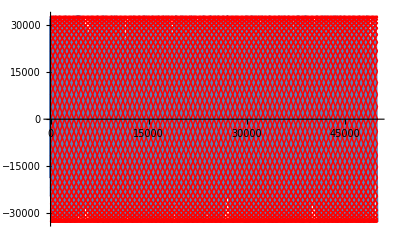

```mathematica
sample=GenerateSamples[{{Cos[2π*173.05"t"],0,50}},{1000,0},{32767,0}];
```

```mathematica
LoadSingleReplayModeSamples[{sample},$SpcmDev]
```

0

```mathematica
SequenceFile["Sequence/Raman.seq",{"Cooling"[1000],"Zero"[1],"Pumping"[5],"AWG"[1],"Raman"[1],"Detection"[300,1,1],"Zero"[1]}]
```

D:\Data\Sequence\Raman.seq

```mathematica
SpcmVClose[$SpcmDev];(*disconnect*)
ClearAll[$SpcmDev];
```